# Diversity at the United World Colleges

The United World Colleges (UWC) are a group of currently 17 schools and National committees in 155 countries all around the world providing these high schools with the majority of their students. Initially founded in 1962 in Wales by German pedagogue Kurt Hahn, UWC aims to “make education a force to unite people, nations and cultures for peace and a sustainable future” (UWC Mission Statement). UWC tries to achieve this through several means, one important one being the diversity of the movement. In the following exploration, I will attempt to illustrate and measure diversity of UWC.

## Locations of UWC Schools

UWC aims to spread their schools as much across the globe as possible. To explore these locations, I created a dataset of UWCs and several interesting  parameters about them.

Import the dataset of UWC schools

```mathematica
schoolData=SortBy[SemanticImport["C:\\Users\\rbc15\\Desktop\\Mathematica\\WSS2018\\ComputationalEssay\SchoolData.csv"],"UWC since"]
```

Dataset[<>]

The first thing I want to do with this data is making the data easier to read. Below, for example, the Bar Chart makes it a lot easier to see how different in scale UWC South East Asia is to all the other UWC, because they serve a large number of local Singaporean students especially in the lower years.

Make a Chart showing the number of students attending each UWC

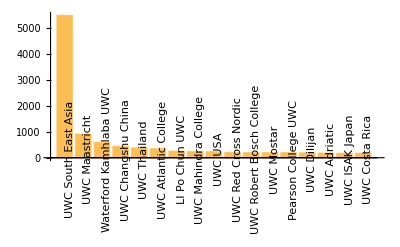

```mathematica
BarChart[ReverseSort[Map[Labeled[#[[2]],Rotate[#[[1]],Pi/2]]&,Normal[schoolData[All,{1,5}]]]]]
```

Another interesting plot to make is the geographical locations of different UWC schools around the world. The graph below shows, that there is a large concentration of UWC schools in Europe . Most other UWCs are more separated, with significant gaps in Africa, Central Eurasia and South America.

Make a plot of UWC schools’ locations.

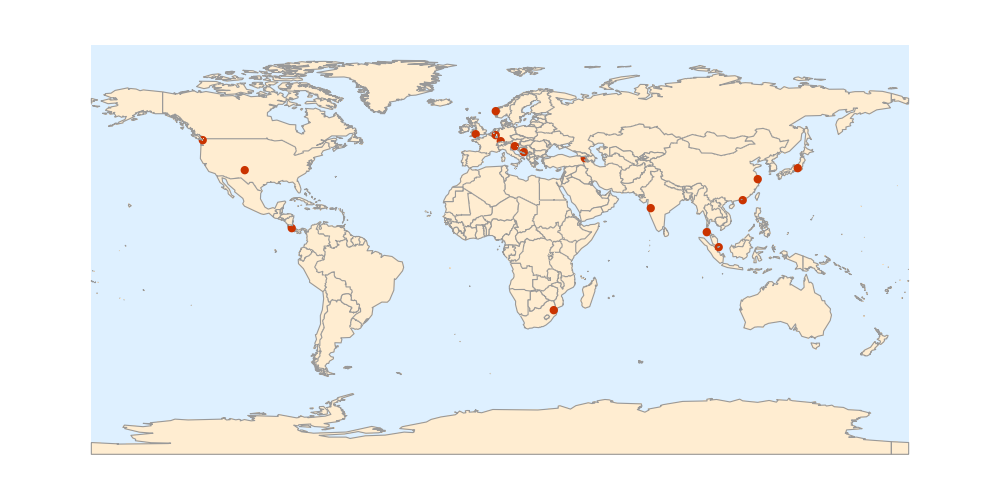

```mathematica
GeoListPlot[EntityValue[{Entity["AdministrativeDivision",{"ValeOfGlamorganThe","Wales","UnitedKingdom"}],Entity["City",{"Freiburg","BadenWurttemberg","Germany"}],Entity["City",{"SantaAna","SanJose","CostaRica"}],Entity["City",{"Pune","Maharashtra","India"}],Entity["City",{"Flekke","SognOgFjordane","Norway"}],Entity["City",{"Maastricht","Limburg","Netherlands"}] ,Entity["City",{"Karuizawa","Nagano","Japan"}],Entity["City",{"Singapore","Singapore","Singapore"}],Entity["AdministrativeDivision",{"DuinoAurisina","Trieste","FriuliVeneziaGiulia","Italy"}],Entity["City",{"Mostar","FederacijaBosnaIHercegovina","BosniaHerzegovina"}],Entity["City",{"HongKong","HongKong","HongKong"}], Entity["City",{"LasVegas","NewMexico","UnitedStates"}], Entity["City",{"Phuket","Phuket","Thailand"}], Entity["City",{"Mbabane","Hhohho","Swaziland"}],Entity["City",{"Victoria","BritishColumbia","Canada"}], Entity["City",{"Dilijan","Tavush","Armenia"}],Entity["City",{"Changshu","Jiangsu","China"}]},"Position"],GeoBackground->"CountryBorders",ImageSize->1000]
```

## Student Origin

Some of the UWC schools serve students for more than the two years of the International Baccalaureate Diploma Programme (IBDP), but those two years are the most essential, since they are the students selected by National Committees, most fulfilling the mission of UWC. I contacted the International Office of UWC and they were able to provide me with a dataset about the students attending UWC from different National Committees in the last three years.

Import the dataset on Students from different National Committees.

```mathematica
studentData = SemanticImport["C:\\Users\\rbc15\\Desktop\\Mathematica\\WSS2018\\ComputationalEssay\\IBDP students by country (3) .csv"]
```

Dataset[<>]

One interesting thing to do with this data is looking at the coverage of the national committees. As seen in the map below, UWC selects students from almost every country, gaps exist only in the Sahara region (which already has low population density) and in other countries like North Korea. Some of these have small population numbers, randomizing the question whether there is a UWC student from the given country, others have political issues that may misalign them with UWC’s values.

Make a map of countries from which students attend UWC

```mathematica
GeoListPlot[DeleteDuplicates[studentData[All,3]],ImageSize->1000]
```

-Graphics-

However, the map above does not tell us enough about the actual diversity of the UWC students yet. There could be one student from each country, except for Madagascar, which provides all the other students. We could not tell from the graph. 
Below there is a better graph showing a

```mathematica
GeoRegionValuePlot[GroupBy[studentData[All,{3,5}],Lookup["Country (groups)"]->Last,Total],ImageSize->1000,GeoBackground->"CountryBorders",ColorFunction->(ColorData["SunsetColors"][#]&)]
```

-Graphics-

```mathematica
GeoRegionValuePlot[Association[KeyValueMap[#1->Divide[#2,#1["Population"]//QuantityMagnitude//N]&,GroupBy[Normal[studentData[All,{3,5}]],Lookup["Country (groups)"]->Last,Total]]]//Log, ImageSize->1000,GeoBackground-> "CountryBorders",ColorFunction->(ColorData["SunsetColors"][#]&)]
```

-Graphics-